# Neural Network About Titanic Survived

### https : // www . bilibili . com/video/BV1Wa411e7dk

### https : // www . wolfram . com/wolfram - u/catalog/wl035/

```mathematica
titanicdata=ExampleData[{"Dataset","Titanic"}];
titanicdata=DeleteMissing[titanicdata,1,2];
{trainingData,testData}=TakeDrop[RandomSample@titanicdata,800]
```

{,}

```mathematica
classEncoder=NetEncoder[{"Class",{"1st","2nd","3rd"},"UnitVector"}]
genderEncoder=NetEncoder[{"Class",{"male","female"},"UnitVector"}]
```

NetEncoder[<>]

NetEncoder[<>]

```mathematica
net1=NetGraph[{CatenateLayer[]},{{NetPort["class"],NetPort["age"],NetPort["sex"]}->1},"class"->classEncoder,"age"->"Scalar","sex"->genderEncoder]
```

NetGraph[<>]

```mathematica
net2=NetGraph[{net1,LinearLayer[],LogisticSigmoid},{1->2->3->NetPort["survived"]},"survived"->"Boolean"]
```

NetGraph[<>]

```mathematica
trained=NetTrain[net2,trainingData,MaxTrainingRounds->1000]
```

NetGraph[<>]

```mathematica
{trained[<|"class"->"1st","age"->20,"sex"->"female"|>],trained[<|"class"->"1st","age"->20,"sex"->"female"|>,None]}
{trained[<|"class"->"3rd","age"->30,"sex"->"male"|>],trained[<|"class"->"3rd","age"->30,"sex"->"male"|>,None]}
```

{True,0.951568}

{False,0.0961094}

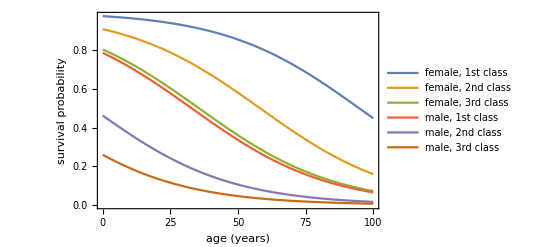

```mathematica
p[class_,age_,sex_]:=trained[<|"class"->class,"age"->age,"sex"->sex|>,None];
Plot[{p["1st",x,"female"],p["2nd",x,"female"],p["3rd",x,"female"],p["1st",x,"male"],p["2nd",x,"male"],p["3rd",x,"male"]},{x,0,100},PlotLegends->{"female, 1st class","female, 2nd class","female, 3rd class","male, 1st class","male, 2nd class","male, 3rd class"},Frame->True,FrameLabel->{"age (years)","survival probability"}]
```

```mathematica
cm=ClassifierMeasurements[trained,testData->"survived","Accuracy"]
cf=Classify[trainingData->"survived"];
ClassifierMeasurements[cf,testData->"survived","Accuracy"]
```

0.792683

0.792683

```mathematica
LinguisticAssistant
```

Failure[…]

```mathematica
Entity["Word","neural"]
```